### Check ChiQ A B E Katrina PV

```mathematica
vweekKatPV = ReadList["/Users/Levantina/Documents/FISICA/TESIPOP/Timeseries2/KatrinaPVTSweek.txt"];
```

```mathematica
logvweekKatPV  = ReadList["/Users/Levantina/Documents/FISICA/TESIPOP/Timeseries2/KatrinaPVTSlogweek.txt"];
```

```mathematica
t0= 50;
```

```mathematica
te = 64;
```

#### Chi Squared critical values

Qui prendiamo i valori critici per il test del chi quadro standard, abbiamo due tavole, una per i valori critici superiori ed una per i valori critici inferiori, scegliamo il livello di singificatività (nell’ordine per α/2 che vale 0.1, 0.05, 0.025, 0.01, 0.001 - le colonne) ed il numero di gradi di libertà (le righe dalla 1 alla 80).

```mathematica
upperTail = Flatten[StringSplit[#]&/@ Import["/Users/Levantina/Documents/FISICA/TESIPOP/ChiQ/upperTail.tsv"],1];
```

```mathematica
lowerTail = Flatten[StringSplit[#]&/@ Import["/Users/Levantina/Documents/FISICA/TESIPOP/ChiQ/lowerTail.tsv"],1];
```

#### Print on file Model 1 and 2

```mathematica
chiQ1AllKat=Transpose[{Chi1KatLogB15,Chi1KatLogE15,Chi1KatLogA15}];
```

```mathematica
Export["/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/chiQ1AllKatPV.txt",chiQ1AllKat]
```

/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/chiQ1AllKatPV.txt

```mathematica
chiQ2AllKat=Transpose[{Chi2KatLogB15,Chi2KatLog15,Chi2KatLogA15}];
```

```mathematica
Export["/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/chiQ2AllKatPV.txt",chiQ2AllKat]
```

/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/chiQ2AllKatPV.txt

```mathematica
chiQ1AllKat =ReadList["/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/chiQ1AllKatPV.txt"];
```

```mathematica
chiQ2AllKat = ReadList["/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/chiQ2AllKatPV.txt"];
```

#### Rimuovo i NoData con {0,0} per aggiustare la corrispondenza degli indici

```mathematica
Length@Chi1KatLogB15
```

635

```mathematica
Length@logvweekKatPV
```

635

```mathematica
Length@Chi1KatLogA15
```

635

```mathematica
Length@Chi1KatLogE15
```

635

#### Selction in 4 groups

```mathematica
Tally[Chi1KatLogB15[[All,2]]]
```

{{49,624},{0.,2},{35,1},{33,1},{48,2},{19,1},{4,2},{40,1},{9,1}}

```mathematica
Tally[Chi1KatLogA15[[All,2]]]
```

{{40,632},{29,1},{6,1},{35,1}}

```mathematica
Tally[Chi1KatLogE15[[All,2]]]
```

{{15,630},{0.,1},{6,1},{13,1},{4,1},{12,1}}

```mathematica
SelectGroupChiQBEA[chiB_List, chiE_List, chiA_List] := Module[{chiBEA, acceptBEA, upcrit, lowcrit, notAnalyzed,
	TA, TB, TE, posA, posB, posE, posAB, chiAB, 
	uA, lA, uB, lB, uE, lE},
TB = Tally[chiB[[All,2]]][[1,1]];
TA = Tally[chiA[[All,2]]][[1,1]];
TE = Tally[chiE[[All,2]]][[1,1]];
posB = Position[chiB,{__,TB}];
posA = Position[chiA,{__,TA}];
posE = Position[chiE,{__,TE}];
posAB = Intersection[posB,posA,posE];
uA = ToExpression[upperTail[[TA-2,4]]];
lA = ToExpression[lowerTail[[TA-2,4]]];
uB = ToExpression[upperTail[[TB-2,4]]];
lB = ToExpression[lowerTail[[TB-2,4]]];
uE = ToExpression[upperTail[[TE,4]]];
lE = ToExpression[lowerTail[[TE,4]]];

chiBEA = Transpose[{chiB,chiE,chiA}];
acceptBEA = DeleteCases[If[((#[[1,1]] > lB && #[[1,1]] < uB ) && (#[[3,1]] > lA && #[[3,1]] < uA ) && (#[[2,1]] > lE && #[[2,1]] < uE)),#,No]& /@ chiBEA[[Flatten@posAB]],No];
lowcrit = DeleteCases[If[((#[[1,1]] > lB && #[[1,1]] < uB ) && (#[[3,1]] > lA && #[[3,1]] < uA ) && (#[[2,1]] < lE)),#,No]& /@ chiBEA[[Flatten@posAB]],No];
upcrit = DeleteCases[If[((#[[1,1]] > lB && #[[1,1]] < uB ) && (#[[3,1]] > lA && #[[3,1]] < uA ) && (#[[2,1]] > uE)),#,No]& /@ chiBEA[[Flatten@posAB]],No];
notAnalyzed = chiBEA[[Complement[Range[Length@chiB],Flatten@Union[(Flatten@Position[chiBEA,#]&/@ acceptBEA),
	(Flatten@Position[chiBEA,#]&/@ lowcrit),
	(Flatten@Position[chiBEA,#]&/@ upcrit)]]]];

{{TB-2,TA-2,TE},
	Flatten@Position[chiBEA,#]&/@ acceptBEA,
	Flatten@Position[chiBEA,#]&/@ lowcrit,
	Flatten@Position[chiBEA,#]&/@ upcrit,
	Flatten@Position[chiBEA,#]&/@ notAnalyzed,
	posAB, 
	chiBEA}
]

(* la colonna 4 in upperTail / lowerTail si riferisce al valore di sgnifiatività del test di 0.05 
in output abbiamo al primo termine i gradi di libertà di ChiQB e ChiQA e di ChiQE (event), 
al secondo gli indici delle pagine accettabili (col maggior numero di gradi di libertà),
al terzo gli indici delle lowercritic, al quarto gli indici delle pagine uppercritic, al quinto gli indici delle pagine notAnalyzed, 
ed al sesto abbiamo le triplette di TUTTI i chiQ. Gli indici si riferiscono alla sequenza originaria delle pagine. *)
```

### MODEL 1

```mathematica
Chi1KatLogB15 = chiQ1AllKat[[All,1]];
```

```mathematica
Chi1KatLogE15 = chiQ1AllKat[[All,2]];
```

```mathematica
Chi1KatLogA15 = chiQ1AllKat[[All,3]];
```

```mathematica
ris1K=SelectGroupChiQBEA[Chi1KatLogB15,Chi1KatLogE15,Chi1KatLogA15 ];
```

#### Scatter Plot 4 groups VS Correlation

INDICI:
2) accept
3) lower crit
4) upper crit
5) not nalyzed

```mathematica
corrKPV=ReadList["/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/corrKatPVNoZero.txt"];
```

```mathematica
firstG=Transpose[{corrKPV[[Flatten@ris1K[[2]]]],Log@ris1K[[7,Flatten@ris1K[[2]],2,1]]}];
```

```mathematica
secondG=Transpose[{corrKPV[[Flatten@ris1K[[3]]]],Log@ris1K[[7,Flatten@ris1K[[3]],2,1]]}];
```

```mathematica
thirdG= Transpose[{corrKPV[[Flatten@ris1K[[4]]]],Log@ris1K[[7,Flatten@ris1K[[4]],2,1]]}];
```

```mathematica
fourthG= Transpose[{corrKPV[[Flatten@ris1K[[5]]]],Log@ris1K[[7,Flatten@ris1K[[5]],2,1]]}];
```

```mathematica
Position[fourthG[[All,1]],-0.2899784623016133]
```

{{73}}

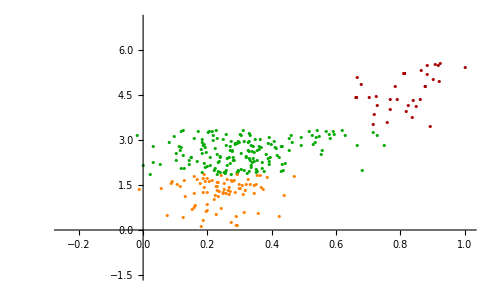

```mathematica
ListPlot[{firstG,secondG,thirdG,Delete[fourthG,{73}]},PlotRange->{{-0.25,1.01},{-1.5,7}},PlotStyle->{Darker@Green,Orange,Darker@Red,Black},PlotMarkers->{•,•,•,•,Small},PlotLegends->Placed[{"Acceptable","Lower Critical","Upper Critical","Not Analyzed"},{0.09,0.87}],AxesLabel->{"C_(1  p)","Log (χ_p^2()_1)^E"},PlotLabel->"FN Katrina"]
```

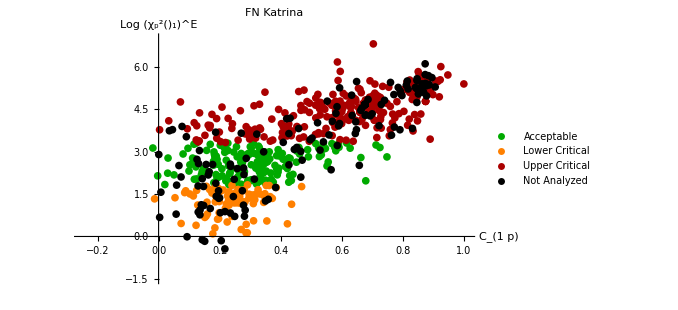

```mathematica
ListPlot[{firstG,secondG,thirdG,Delete[fourthG,{73}]},PlotRange->{{-0.25,1.01},{-1.5,7}},PlotStyle->{{PointSize[0.011],Darker@Green},{PointSize[0.011],Orange},{PointSize[0.011],Darker@Red},{PointSize[0.011],Black}},PlotLegends->Placed[{"Acceptable","Lower Critical","Upper Critical","Not Analyzed"},{0.09,0.87}],AxesLabel->{"C_(1  p)","Log (χ_p^2()_1)^E"},PlotLabel->"FN Katrina"]
```

#### Histogram ChiQE solo per le pagine analizzate

```mathematica
analyzed1PV=Union[Flatten@ris1K[[2]],Flatten@ris1K[[3]],Flatten@ris1K[[4]]];
```

```mathematica
Length@analyzed1PV
```

489

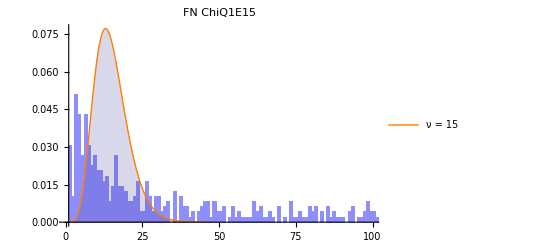

```mathematica
Show[Histogram[Chi1KatLogE15[[analyzed1PV,1]],{1},"Probability",ChartStyle->Lighter@Lighter@Blue],StandardChiQDistr[15],PlotLabel->"FN ChiQ1E15",PlotRange->{{0,100},{All,All}}]
```

```mathematica
Length@Select[Chi1KatLogE15[[analyzed1PV,1]],#>100&]
```

92

```mathematica
Sort@Select[Chi1KatLogE15[[analyzed1PV,1]],#>100&]
```

{100.027,100.285,101.747,102.215,103.018,103.875,104.023,104.47,107.012,107.87,110.063,110.396,110.949,111.317,111.959,113.499,113.988,114.585,114.623,114.977,116.323,117.128,118.197,118.611,119.601,119.601,119.928,120.071,120.171,120.491,120.685,124.478,125.577,127.779,128.744,133.521,134.468,136.951,137.243,138.324,140.2,141.923,144.798,144.897,145.869,146.448,149.032,151.693,152.612,153.151,153.203,158.338,159.548,162.268,163.768,165.495,169.25,170.227,175.366,175.727,175.93,178.074,178.874,183.112,184.178,184.178,184.178,189.865,196.974,200.924,203.312,212.663,220.345,221.395,226.051,227.415,235.661,240.767,241.989,245.314,247.503,250.36,252.506,254.11,256.211,304.242,314.76,342.43,345.144,408.735,481.541,913.955}

### Plot tracce dei 3 gruppi

#### Accettabili

```mathematica
RGBColor[0.996078431372549,0.9882352941176471,0.03529411764705882]
```

RGBColor[0.996078,0.988235,0.0352941]

```mathematica
Length@ColorData[3,"ColorList"]
```

10

```mathematica
opt={Thickness[0.005],#}&/@ColorData[3,"ColorList"]
```

{{Thickness[0.005],RGBColor[0.,0.,0.]},{Thickness[0.005],RGBColor[0.996078,0.360784,0.027451]},{Thickness[0.005],RGBColor[0.996078,0.988235,0.0352941]},{Thickness[0.005],RGBColor[0.541176,0.713725,0.027451]},{Thickness[0.005],RGBColor[0.145098,0.435294,0.384314]},{Thickness[0.005],RGBColor[0.00784314,0.509804,0.929412]},{Thickness[0.005],RGBColor[0.152941,0.113725,0.490196]},{Thickness[0.005],RGBColor[0.470588,0.262745,0.584314]},{Thickness[0.005],RGBColor[0.890196,0.0117647,0.490196]},{Thickness[0.005],RGBColor[0.905882,0.027451,0.129412]}}

{{Thickness[0.005],RGBColor[0.,0.26,0.15]},{Thickness[0.005],RGBColor[0.996078,0.360784,0.027451]},{Thickness[0.005],RGBColor[0.01,0.28,1.]},{Thickness[0.005],RGBColor[0.541176,0.713725,0.027451]},{Thickness[0.005],RGBColor[0.145098,0.435294,0.384314]},{Thickness[0.005],RGBColor[0.00784314,0.509804,0.929412]},{Thickness[0.005],RGBColor[0.152941,0.113725,0.490196]},{Thickness[0.005],RGBColor[0.470588,0.262745,0.584314]},{Thickness[0.005],RGBColor[0.890196,0.0117647,0.490196]},{Thickness[0.005],RGBColor[0.905882,0.027451,0.129412]}}

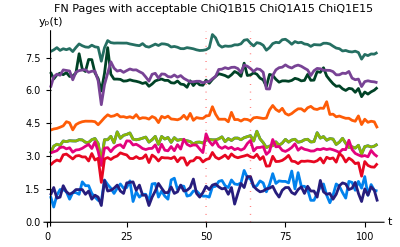

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris1K[[2]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN Pages with acceptable ChiQ1B15 ChiQ1A15 ChiQ1E15",PlotStyle->opt1],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

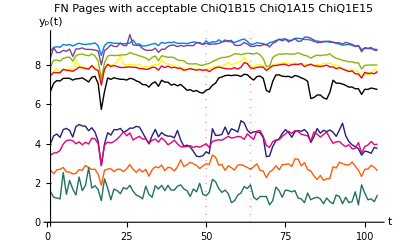

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris1K[[2]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN Pages with acceptable ChiQ1B15 ChiQ1A15 ChiQ1E15",PlotStyle->ColorData[3,"ColorList"]],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Lower crit

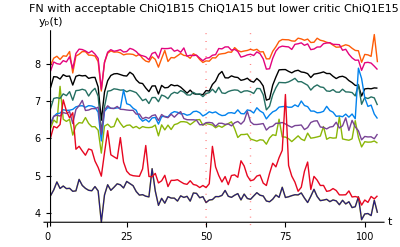

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris1K[[3]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN with acceptable ChiQ1B15 ChiQ1A15 but lower critic ChiQ1E15",PlotStyle->ColorData[3,"ColorList"]],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

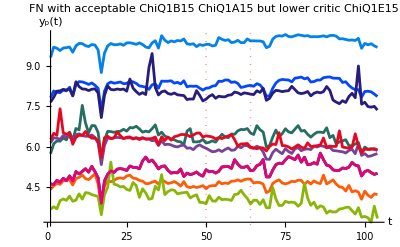

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris1K[[3]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN with acceptable ChiQ1B15 ChiQ1A15 but lower critic ChiQ1E15",PlotStyle->opt1],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Upper crit

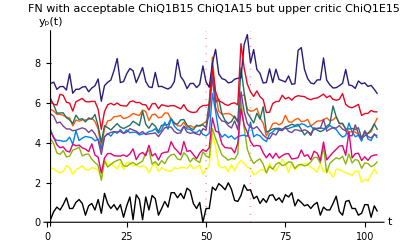

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris1K[[4]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with acceptable ChiQ1B15 ChiQ1A15 but upper critic ChiQ1E15"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

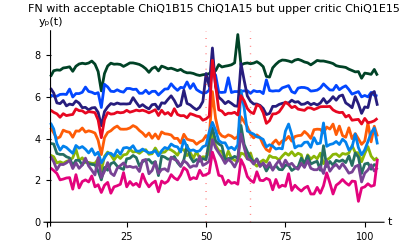

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris1K[[4]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->opt1,PlotLabel->"FN with acceptable ChiQ1B15 ChiQ1A15 but upper critic ChiQ1E15"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Not Analyzed

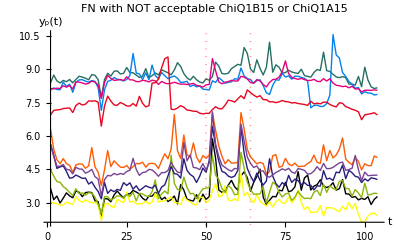

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris1K[[5]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ1B15 or ChiQ1A15"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

### Correlation Thresholds

#### Not Analyzed 3 groups C_ij^upper= 0.6 (random-random)

Punti neri con C_ij >= 0.6

```mathematica
blackCbig06=Select[If[corrKPV[[#]]>=0.6,#,No]&/@ Flatten@ris1K[[5]],NumberQ];
```

```mathematica
Length@blackCbig06
```

76

Punti neri con C_ij < 0.6

```mathematica
blackCaccept06=Select[If[corrKPV[[#]]<0.6,#,No]&/@ Flatten@ris1K[[5]],NumberQ];
```

```mathematica
Length@blackCaccept06
```

89

Punti rossi con C_ij < 0.6

```mathematica
redCaccept06=Select[If[corrKPV[[#]]<0.6,#,No]&/@ Flatten@ris1K[[4]],NumberQ];
```

```mathematica
Length@redCaccept06
```

113

Grafici

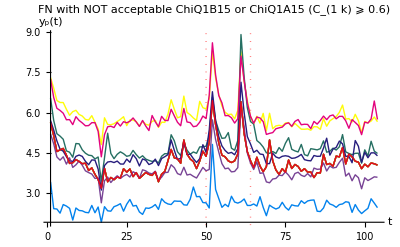

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[blackCbig06,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ1B15 or ChiQ1A15 (C_(1  k) ⩾ 0.6)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

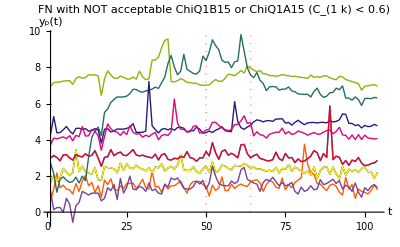

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[blackCaccept06,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ1B15 or ChiQ1A15 (C_(1  k) < 0.6)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

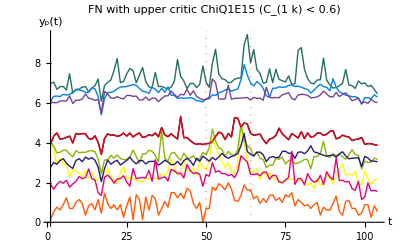

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[redCaccept06,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with upper critic ChiQ1E15 (C_(1  k) < 0.6)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Not Analyzed 3 groups C_ij^upper= 0.3 (katrina-random)

Punti neri con C_ij > 0.0

```mathematica
blackCbig03=Select[If[corrKPV[[#]]>0.3,#,No]&/@ Flatten@ris1K[[5]],NumberQ];
```

```mathematica
Length@blackCbig03
```

108

Punti neri con C_ij < 0.3

```mathematica
blackCaccept03=Select[If[corrKPV[[#]]<=0.3,#,No]&/@ Flatten@ris1K[[5]],NumberQ];
```

```mathematica
Length@blackCaccept03
```

57

Punti rossi con C_ij < 0.3

```mathematica
redCaccept03=Select[If[corrKPV[[#]]<=0.3,#,No]&/@ Flatten@ris1K[[4]],NumberQ];
```

```mathematica
Length@redCaccept03
```

32

Grafici

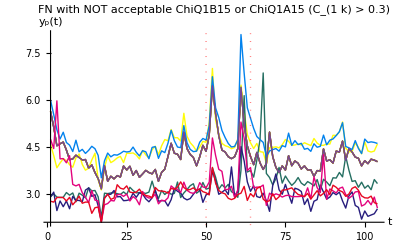

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[blackCbig03,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ1B15 or ChiQ1A15 (C_(1  k) > 0.3)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

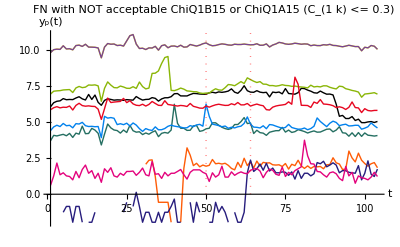

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[blackCaccept03,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ1B15 or ChiQ1A15 (C_(1  k) <= 0.3)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

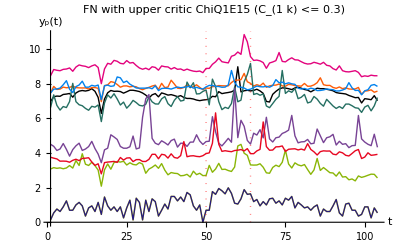

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[redCaccept03,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with upper critic ChiQ1E15 (C_(1  k) <= 0.3)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Not Analyzed 3 groups C_ij^upper= 0.4 (compromise)

Punti neri con C_ij >= 0.4

```mathematica
blackCbig04=Select[If[corrKPV[[#]]>=0.4,#,No]&/@ Flatten@ris1K[[5]],NumberQ];
```

```mathematica
Length@blackCbig04
```

102

Punti neri con C_ij < 0.4

```mathematica
blackCaccept04=Select[If[corrKPV[[#]]<0.4,#,No]&/@ Flatten@ris1K[[5]],NumberQ];
```

```mathematica
Length@blackCaccept04
```

63

Punti rossi con C_ij < 0.4

```mathematica
redCaccept04=Select[If[corrKPV[[#]]<0.4,#,No]&/@ Flatten@ris1K[[4]],NumberQ];
```

```mathematica
Length@redCaccept04
```

45

Grafici

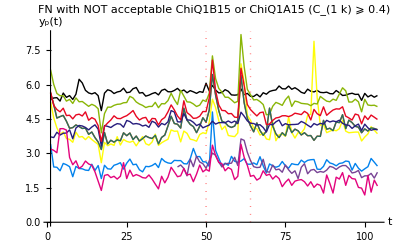

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[blackCbig04,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ1B15 or ChiQ1A15 (C_(1  k) ⩾ 0.4)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

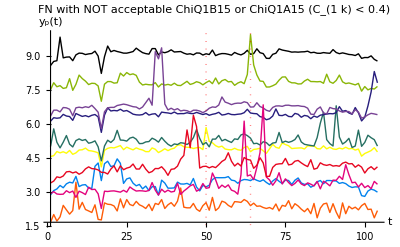

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[blackCaccept04,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ1B15 or ChiQ1A15 (C_(1  k) < 0.4)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

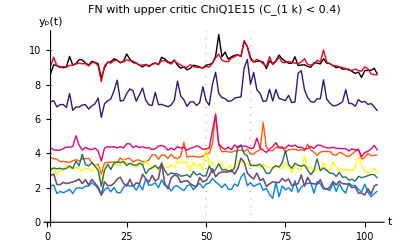

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[redCaccept04,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with upper critic ChiQ1E15 (C_(1  k) < 0.4)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

### MODEL 2

```mathematica
Chi2KatLogB15 = chiQ2AllKat[[All,1]];
```

```mathematica
Chi2KatLog15 = chiQ2AllKat[[All,2]];
```

```mathematica
Chi2KatLogA15 = chiQ2AllKat[[All,3]];
```

```mathematica
ris2K=SelectGroupChiQBEA[Chi2KatLogB15,Chi2KatLog15,Chi2KatLogA15];
```

#### Scatter Plot 4 groups VS Correlation

INDICI:
2) accept
3) lower crit
4) upper crit
5) not nalyzed

```mathematica
corrKPV=ReadList["/Users/Levantina/Documents/FISICA/TESIPOP/KatrinaPVSV/corrKatPVNoZero.txt"];
```

```mathematica
firstG2=Transpose[{corrKPV[[Flatten@ris2K[[2]]]],Log@ris2K[[7,Flatten@ris2K[[2]],2,1]]}];
```

```mathematica
secondG2=Transpose[{corrKPV[[Flatten@ris2K[[3]]]],Log@ris2K[[7,Flatten@ris2K[[3]],2,1]]}];
```

```mathematica
thirdG2= Transpose[{corrKPV[[Flatten@ris2K[[4]]]],Log@ris2K[[7,Flatten@ris2K[[4]],2,1]]}];
```

```mathematica
fourthG2= Transpose[{corrKPV[[Flatten@ris2K[[5]]]],Log@ris2K[[7,Flatten@ris2K[[5]],2,1]]}];
```

```mathematica
Position[fourthG2[[All,1]],-0.2899784623016133]
```

{{146}}

```mathematica
ListPlot[{firstG2,secondG2,thirdG2,Delete[fourthG2,{146}]},PlotRange->{{-0.25,1.01},{-2,8}},PlotStyle->{Darker@Green,Orange,Darker@Red,Black},PlotMarkers->{•,•,•,•,Small},PlotLegends->Placed[{"Acceptable","Lower Critical","Upper Critical","Not Analyzed"},{0.09,0.87}],AxesLabel->{"C_(1  p)","Log (χ_p^2()_2)^E"},PlotLabel->"FN Katrina"]
```

#### Histogram ChiQE solo per le pagine analizzate

```mathematica
analyzed2PV=Union[Flatten@ris2K[[2]],Flatten@ris2K[[3]],Flatten@ris2K[[4]]];
```

```mathematica
Length@analyzed2PV
```

420

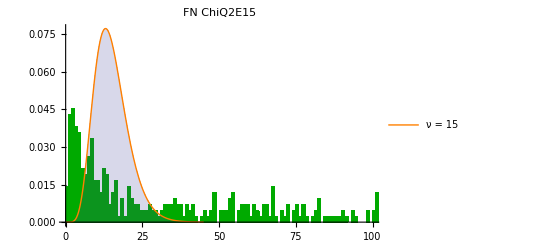

```mathematica
Show[Histogram[Chi2KatLog15[[analyzed2PV,1]],{1},"Probability",ChartStyle->Darker@Green],StandardChiQDistr[15],PlotLabel->"FN ChiQ2E15",PlotRange->{{0,100},{All,All}}]
```

```mathematica
Length@Select[Chi2KatLog15[[analyzed2PV,1]],#>100&]
```

91

```mathematica
Sort@Select[Chi2KatLog15[[analyzed2PV,1]],#>100&]
```

{100.014,100.567,101.854,101.854,101.854,101.854,101.854,102.428,102.546,105.195,105.195,106.631,108.881,110.989,111.311,111.449,114.158,115.149,118.215,119.525,119.599,120.194,121.458,122.284,122.359,126.701,128.872,129.375,129.605,130.258,132.56,135.121,135.43,135.43,135.474,138.375,140.017,145.348,146.586,146.659,149.128,156.786,161.359,162.99,163.133,163.261,172.928,175.448,180.615,181.432,182.059,182.494,182.77,183.55,185.614,189.487,189.487,189.487,189.664,191.021,191.71,199.179,203.952,203.967,207.731,211.165,215.711,222.653,224.689,226.403,230.546,234.877,236.121,236.778,243.119,248.545,250.325,251.157,257.92,261.655,262.884,263.063,265.271,290.429,297.603,310.962,336.633,355.061,378.028,378.028,437.728}

### Plot tracce dei 3 gruppi

#### Accettabili

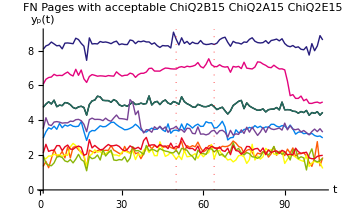

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris2K[[2]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN Pages with acceptable ChiQ2B15 ChiQ2A15 ChiQ2E15",PlotStyle->ColorData[3,"ColorList"]],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

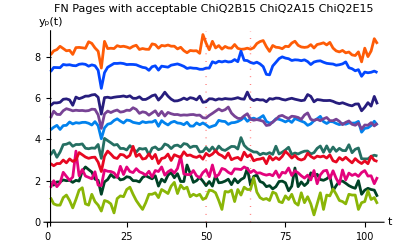

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris2K[[2]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN Pages with acceptable ChiQ2B15 ChiQ2A15 ChiQ2E15",PlotStyle->opt1],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Lower crit

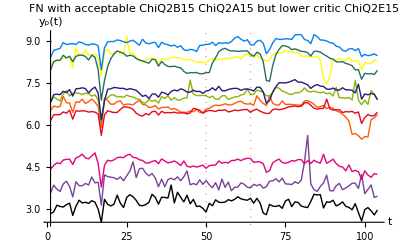

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris2K[[3]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN with acceptable ChiQ2B15 ChiQ2A15 but lower critic ChiQ2E15",PlotStyle->ColorData[3,"ColorList"]],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

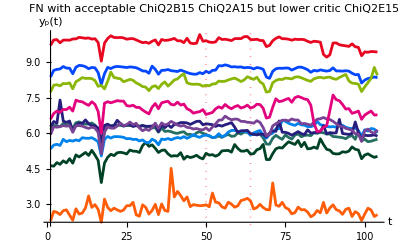

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris2K[[3]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotLabel->"FN with acceptable ChiQ2B15 ChiQ2A15 but lower critic ChiQ2E15",PlotStyle->opt1],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Upper crit

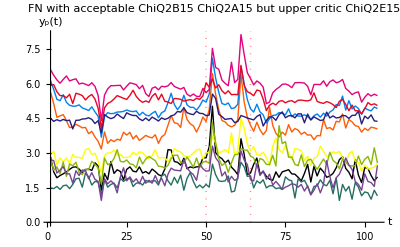

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris2K[[4]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with acceptable ChiQ2B15 ChiQ2A15 but upper critic ChiQ2E15"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

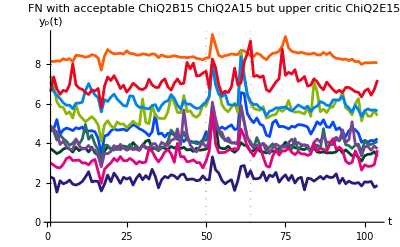

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris2K[[4]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->opt1,PlotLabel->"FN with acceptable ChiQ2B15 ChiQ2A15 but upper critic ChiQ2E15"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Not Analyzed

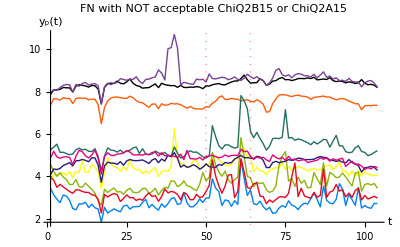

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@RandomChoice[Flatten@ris2K[[5]],10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ2B15 or ChiQ2A15"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

### Correlation Thresholds

#### Not Analyzed 3 groups C_ij^upper= 0.6 (random-random)

Punti neri con C_ij >= 0.6

```mathematica
black2Cbig06=Select[If[corrKPV[[#]]>=0.6,#,No]&/@ Flatten@ris2K[[5]],NumberQ];
```

```mathematica
Length@black2Cbig06
```

42

Punti neri con C_ij < 0.6

```mathematica
black2Caccept06=Select[If[corrKPV[[#]]<0.6,#,No]&/@ Flatten@ris2K[[5]],NumberQ];
```

```mathematica
Length@black2Caccept06
```

172

Punti rossi con C_ij < 0.6

```mathematica
red2Caccept06=Select[If[corrKPV[[#]]<0.6,#,No]&/@ Flatten@ris2K[[4]],NumberQ];
```

```mathematica
Length@red2Caccept06
```

85

Grafici

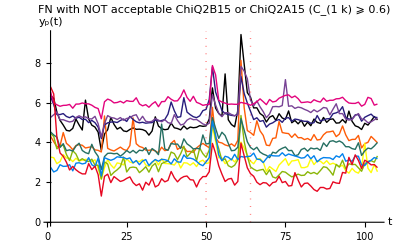

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[black2Cbig06,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ2B15 or ChiQ2A15 (C_(1  k) ⩾ 0.6)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

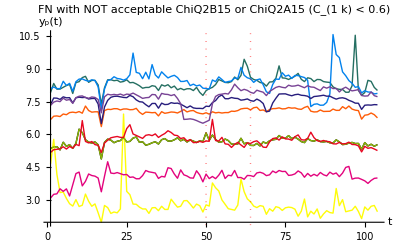

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[black2Caccept06,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ2B15 or ChiQ2A15 (C_(1  k) < 0.6)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

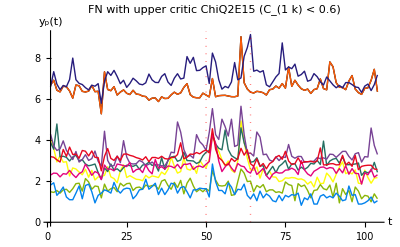

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[red2Caccept06,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with upper critic ChiQ2E15 (C_(1  k) < 0.6)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

#### Not Analyzed 3 groups C_ij^upper= 0.4 (compromise)

Punti neri con C_ij >= 0.4

```mathematica
black2Cbig04=Select[If[corrKPV[[#]]>=0.4,#,No]&/@ Flatten@ris2K[[5]],NumberQ];
```

```mathematica
Length@black2Cbig04
```

86

```mathematica
86*100/635.
```

13.5433

Punti neri con C_ij < 0.4

```mathematica
black2Caccept04=Select[If[corrKPV[[#]]<0.4,#,No]&/@ Flatten@ris2K[[5]],NumberQ];
```

```mathematica
Length@black2Caccept04
```

128

Punti rossi con C_ij < 0.4

```mathematica
red2Caccept04=Select[If[corrKPV[[#]]<0.4,#,No]&/@ Flatten@ris2K[[4]],NumberQ];
```

```mathematica
Length@red2Caccept04
```

22

Grafici

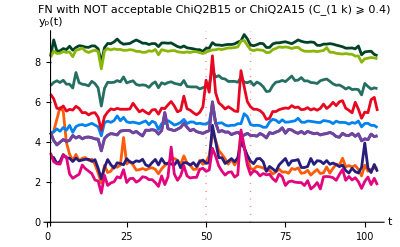

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[black2Cbig04,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->opt1,PlotLabel->"FN with NOT acceptable ChiQ2B15 or ChiQ2A15 (C_(1  k) ⩾ 0.4)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

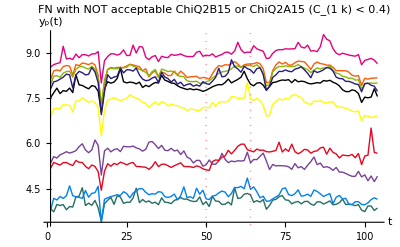

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[black2Caccept04,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->ColorData[3,"ColorList"],PlotLabel->"FN with NOT acceptable ChiQ2B15 or ChiQ2A15 (C_(1  k) < 0.4)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

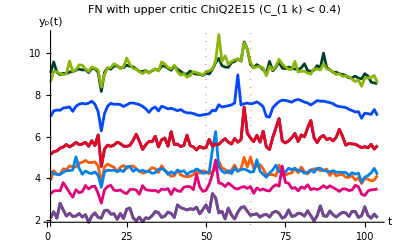

```mathematica
Show[ListLinePlot[logvweekKatPV[[#]]& /@ RandomChoice[red2Caccept04,10],AxesLabel->{"t","y_p(t)"},PlotRange->{All,{0,Max}},PlotStyle->opt1,PlotLabel->"FN with upper critic ChiQ2E15 (C_(1  k) < 0.4)"],
ListLinePlot[{{{t0,0},{t0,12}},{{te,0},{te,12}}},PlotStyle->{{Opacity[0.7],Red,Dotted,Thick},{Opacity[0.7],Red,Dotted,Thick}}]]
```

### Intersection and Union Model 1 & 2 PV

```mathematica
Intersection[Flatten@ris1K[[4]],Flatten@ris2K[[4]]]
```

{1,3,4,5,10,15,21,22,23,24,25,27,28,30,31,33,34,36,38,39,40,42,43,44,47,50,51,54,56,57,58,60,62,63,66,68,69,77,78,83,85,87,91,97,102,106,108,118,123,125,126,127,143,153,154,156,157,158,160,161,164,165,166,168,169,171,172,173,175,176,184,188,189,190,193,196,210,213,232,235,236,237,247,252,269,271,272,273,275,283,285,294,298,310,313,319,325,326,331,345,353,389,391,409,412,415,419,430,435,442,447,452,460,463,478,533,535,537,541,542,543,545,549,555,560,563,564,565,566,568,569,571,572,573,574,575,576,579,581,582,584,585,587,588,593,595,597,599,600,606,607,608,609,611,612,613,614,615,618,619,626,630,631,633,634}

```mathematica
Length@Intersection[Flatten@ris1K[[4]],Flatten@ris2K[[4]]]
```

165

```mathematica
Union[Flatten@ris1K[[4]],Flatten@ris2K[[4]]]
```

{1,3,4,5,10,14,15,20,21,22,23,24,25,26,27,28,30,31,32,33,34,35,36,38,39,40,42,43,44,46,47,50,51,54,56,57,58,59,60,62,63,65,66,68,69,72,74,77,78,80,83,85,87,90,91,92,95,97,102,104,106,108,109,110,111,112,116,118,120,123,125,126,127,132,136,140,143,148,149,150,152,153,154,155,156,157,158,159,160,161,162,164,165,166,168,169,170,171,172,173,175,176,178,184,186,188,189,190,193,194,196,197,210,213,214,217,218,227,232,235,236,237,240,241,242,247,251,252,254,255,261,263,265,268,269,271,272,273,275,283,285,294,298,300,302,305,308,310,313,314,316,319,325,326,331,336,345,353,356,357,358,359,371,374,375,377,381,383,389,391,393,394,398,403,408,409,412,414,415,419,428,430,435,437,442,444,447,452,454,455,456,457,458,459,460,463,478,488,493,502,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,549,550,551,552,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,587,588,590,591,592,593,594,595,596,597,599,600,601,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,624,625,626,628,630,631,632,633,634,635}

```mathematica
Length@Union[Flatten@ris1K[[4]],Flatten@ris2K[[4]]]
```

291

```mathematica
Complement[Union[Flatten@ris1K[[4]],Flatten@ris2K[[4]]],Intersection[Flatten@ris1K[[4]],Flatten@ris2K[[4]]]]
```

{14,20,26,32,35,46,59,65,72,74,80,90,92,95,104,109,110,111,112,116,120,132,136,140,148,149,150,152,155,159,162,170,178,186,194,197,214,217,218,227,240,241,242,251,254,255,261,263,265,268,300,302,305,308,314,316,336,356,357,358,359,371,374,375,377,381,383,393,394,398,403,408,414,428,437,444,454,455,456,457,458,459,488,493,502,531,532,534,536,538,539,540,544,546,547,550,551,552,554,556,557,558,559,561,562,567,570,577,578,580,583,590,591,592,594,596,601,610,616,617,620,624,625,628,632,635}

```mathematica
Length@Complement[Union[Flatten@ris1K[[4]],Flatten@ris2K[[4]]],Intersection[Flatten@ris1K[[4]],Flatten@ris2K[[4]]]]
```

126